```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
```

```mathematica
ds[1]
```

```mathematica
ts=ds[1,"ConfirmedCases"]
```

TimeSeries[…]

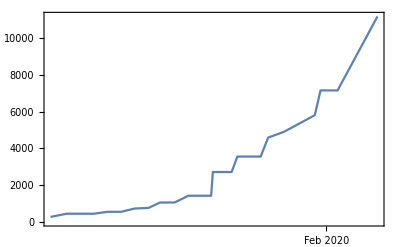

```mathematica
DateListPlot[ts]
```

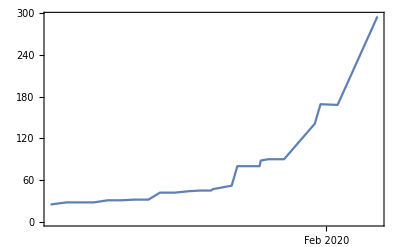

```mathematica
DateListPlot[ds[1,"RecoveredCases"],PlotRange->All]
```

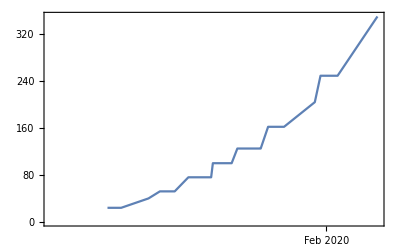

```mathematica
DateListPlot[ds[1,"Deaths"],PlotRange->All]
```

```mathematica
ds[1,"ConfirmedCases"]
```

TimeSeries[…]

```mathematica
ds[1,"ConfirmedCases"]["Values"]
```

{270,444,444,549,549,729,761,1052,1058,1423,1423,1423,2714,2714,3554,3554,3554,3554,4586,4903,5806,7153,7153,11177}

```mathematica
ds[1,"ConfirmedCases"]["Times"]
```

{3788632800,3788683200,3788769600,3788812800,3788856000,3788899200,3788942400,3788978400,3789025200,3789068400,3789104400,3789140400,3789145800,3789205200,3789223200,3789241200,3789293400,3789297000,3789320400,3789370800,3789468000,3789486000,3789540000,3789666000}

```mathematica
ds[1,"ConfirmedCases"]["Dates"]
```

{Tue 21 Jan 2020 22:00:00GMT-6.,Wed 22 Jan 2020 12:00:00GMT-6.,Thu 23 Jan 2020 12:00:00GMT-6.,Fri 24 Jan 2020 00:00:00GMT-6.,Fri 24 Jan 2020 12:00:00GMT-6.,Sat 25 Jan 2020 00:00:00GMT-6.,Sat 25 Jan 2020 12:00:00GMT-6.,Sat 25 Jan 2020 22:00:00GMT-6.,Sun 26 Jan 2020 11:00:00GMT-6.,Sun 26 Jan 2020 23:00:00GMT-6.,Mon 27 Jan 2020 09:00:00GMT-6.,Mon 27 Jan 2020 19:00:00GMT-6.,Mon 27 Jan 2020 20:30:00GMT-6.,Tue 28 Jan 2020 13:00:00GMT-6.,Tue 28 Jan 2020 18:00:00GMT-6.,Tue 28 Jan 2020 23:00:00GMT-6.,Wed 29 Jan 2020 13:30:00GMT-6.,Wed 29 Jan 2020 14:30:00GMT-6.,Wed 29 Jan 2020 21:00:00GMT-6.,Thu 30 Jan 2020 11:00:00GMT-6.,Fri 31 Jan 2020 14:00:00GMT-6.,Fri 31 Jan 2020 19:00:00GMT-6.,Sat 1 Feb 2020 10:00:00GMT-6.,Sun 2 Feb 2020 21:00:00GMT-6.}

```mathematica
UnixTime[]
```

1580935583

```mathematica
AbsoluteTime[]//Round
```

3789902796

```mathematica
FindFit[ds[1,"ConfirmedCases"],a x+b,{a,b},x]
```

{a→0.00912366,b→-3.45678×10^7}

```mathematica
FindFit[ds[1,"ConfirmedCases"],a x+b,{a,b},x]
```

```mathematica
eqn=a x+b/.{a->0.009123657891078704,b->-3.4567805298079826*^7}
```

-3.45678×10^7+0.00912366 x

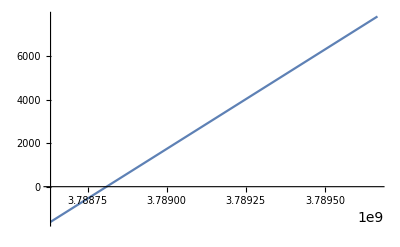

```mathematica
Plot[eqn,{x,3788632800,3789666000}]
```